```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ant/Sites/JumpStartIM/assets/images/functions

```mathematica
ClearAll[PlotPiecewise,PlotPiecewise`plot,PlotPiecewise`init,PlotPiecewise`solve,PlotPiecewise`expand,PlotPiecewise`annotatedPoints,PlotPiecewise`boundaryPoints,PlotPiecewise`interiorPoints,PlotPiecewise`sowAnnotations,PlotPiecewise`inDomain];

PlotPiecewise::usage="PlotPiecewise[Piecewise[...], {x, a, b}, opts]";
PlotPiecewise::limindet="Limit `` is not numeric or infinite at ``";
PlotPiecewise::nonpw="Function `` is not a Piecewise function or did not expand to one";

PlotPiecewise`debug::debug="``";
PlotPiecewise`debug::plot="``";
PlotPiecewise`debug::annotation="``";
PlotPiecewise`debug::limit="``";
PlotPiecewise`debug=Hold[PlotPiecewise`debug::debug,PlotPiecewise`debug::plot,PlotPiecewise`debug::annotation,PlotPiecewise`debug::limit];
Off@@PlotPiecewise`debug;

Options[PlotPiecewise]=Join[{"DotSize"->Automatic,"EmptyDotStyle"->Automatic,"FilledDotStyle"->Automatic,"AsymptoteStyle"->Automatic,"BaseDotSize"->Offset[{2,2}],"AdditionalPoints"->{},(*addition pts to annotate*)"PiecewiseExpand"->Automatic,(*which fns.to expand*)"ContinuousEndpoints"->Automatic},(*eval.formula,not limit*)Options[Plot]];
Options[EmptyDot]=Options[FilledDot]=Options[Asymptote]=Options[PlotPiecewise`plot]=Options[PlotPiecewise`init]=Options[PlotPiecewise];

(*graphics elements*)
Clear[EmptyDot,FilledDot,Asymptote];
EmptyDot[pt_,opts:OptionsPattern[]]/;OptionValue["EmptyDotStyle"]===None:={};
FilledDot[pt_,opts:OptionsPattern[]]/;OptionValue["FilledDotStyle"]===None:={};
Asymptote[pt_,opts:OptionsPattern[]]/;OptionValue["AsymptoteStyle"]===None:={};
EmptyDot[pt_,opts:OptionsPattern[]]:={White,OptionValue["EmptyDotStyle"]/.Automatic->{},Disk[pt,OptionValue["DotSize"]/.Automatic->OptionValue["BaseDotSize"]]};
FilledDot[pt_,opts:OptionsPattern[]]:={OptionValue["FilledDotStyle"]/.Automatic->{},Disk[pt,OptionValue["DotSize"]/.Automatic->OptionValue["BaseDotSize"]]};
Asymptote[x0_,opts:OptionsPattern[]]:={Dashing[Large],OptionValue["AsymptoteStyle"]/.Automatic->{},Line[Thread[{x0,OptionValue[PlotRange][[2]]}]]};


PlotPiecewise`$inequality=Greater|Less|LessEqual|GreaterEqual;
PlotPiecewise`$discontinuousAuto=Ceiling|Floor|Round|Sign;
PlotPiecewise`$discontinuousAll=Ceiling|Floor|Round|Sign|(*Min|Max|Clip|*)UnitStep|IntegerPart|(*FractionalPart|*)Mod|Quotient|UnitBox|UnitTriangle|SquareWave(*|TriangleWave|SawtoothWave*)(*|BernsteinBasis|BSplineBasis|Abs|If|Which|Switch*);
PlotPiecewise`$discontinuous=Ceiling|Floor|Round|Sign;

(*auxiliary functions*)

(*causes Conditional solutions to expand to all possibilities;
(arises from trig eq,and C[1]-- perhaps C[2],etc?*)
PlotPiecewise`expand[cond_Or,var_]:=PlotPiecewise`expand[#,var]&/@cond;
PlotPiecewise`expand[cond_,var_]:=Reduce[cond,var,Backsubstitution->True];
PlotPiecewise`solve[eq_,var_]/;MemberQ[eq,PlotPiecewise`$discontinuous,Infinity,Heads->True]:=PlotPiecewise`solve[#==C[1]&&C[1]∈Integers&&And@@Cases[eq,Except[_Equal]],var]&/@Cases[eq,PlotPiecewise`$discontinuous[e_]:>e,Infinity];
PlotPiecewise`solve[eq_,var_]:={var->(var/.#)}&/@List@ToRules@PlotPiecewise`expand[Reduce[eq,var,Reals,Backsubstitution->True],var]/.{False->{}};

(*limit routines for handling discontinuous functions,which Limit fails to do*)
Needs["NumericalCalculus`"];
PlotPiecewise`nlimit[f_?NumericQ,var_->x0_,dir_]:=f;
PlotPiecewise`nlimit[f_,var_->x0_,dir_]:=NLimit[f,var->x0,dir];
PlotPiecewise`limit[f_,var_->x0_,dir_]/;MemberQ[Numerator[f],PlotPiecewise`$discontinuous,Infinity,Heads->True]:=Module[{y0,f0},f0=f//.(disc:PlotPiecewise`$discontinuous)[z_]/;FreeQ[z,PlotPiecewise`$discontinuous]:>disc[With[{dz=Abs[D[z,var]/.var->N@x0]},Mean[{z/.var->N@x0,z/.var->x0-0.1 Last[dir]/Max[1,dz]}]]];
Message[PlotPiecewise`debug::limit,{f0,f,var->x0,dir}];
Quiet[Check[y0=PlotPiecewise`nlimit[f0,var->x0,dir],Check[y0=Limit[f0,var->x0,dir],If[!NumericQ[y0],y0=Indeterminate]]],{Power::infy,Infinity::indet,NLimit::noise}];
y0];
PlotPiecewise`limit[f_,var_->x0_,dir_]:=Module[{y0},Quiet[Check[y0=f/.var->x0,Check[y0=Limit[f,var->x0,dir],If[!NumericQ[y0],y0=Indeterminate]]],{Power::infy,Infinity::indet}];
y0];

PlotPiecewise`$reverseIneq={Less->Greater,Greater->Less,LessEqual->GreaterEqual};
PlotPiecewise`reverseIneq[(rel:PlotPiecewise`$inequality)[args__]]:=(rel/.PlotPiecewise`$reverseIneq)@@Reverse@{args};
PlotPiecewise`inDomain[]:=LessEqual@@PlotPiecewise`domain[[{2,1,3}]];
PlotPiecewise`inDomain[dom_]:=LessEqual@@dom[[{2,1,3}]];

(*annotatedPoints-- returns list of abscissas to be "annotated" with dots/asymptotes boundaryPoints-- returns list of boundaries numbers between pieces interiorPoints-- returns list of points where the denominator is zero*)
PlotPiecewise`annotatedPoints[allpieces_,domain_,additionalpoints_]:=DeleteDuplicates@Flatten@Join[PlotPiecewise`boundaryPoints[allpieces,domain],PlotPiecewise`interiorPoints[allpieces,domain],additionalpoints];

PlotPiecewise`boundaryPoints[allpieces_,domain:{var_,_,_}]:=With[{conditions=DeleteDuplicates[Equal@@@Flatten[Last/@allpieces/.{HoldPattern@Inequality[a_,rel1_,b_,rel2_,c_]:>{PlotPiecewise`reverseIneq[rel1[a,b]],rel2[b,c]},(rel:PlotPiecewise`$inequality)[a_,b_,c_]:>{PlotPiecewise`reverseIneq[rel[a,b]],rel[b,c]}}]]},Message[PlotPiecewise`debug::annotation,conditions];
var/.Flatten[(*deletes no soln {}'s*)PlotPiecewise`solve[#&&PlotPiecewise`inDomain[domain],var]&/@conditions,1]/.var->{} (*no BPs in domain*)];

PlotPiecewise`interiorPoints[allpieces_,domain:{var_,_,_}]:=MapThread[Function[{formula,condition},Flatten[{With[{solns=PlotPiecewise`solve[Denominator[formula,Trig->True]==0&&(condition/.{LessEqual->Less,GreaterEqual->Greater})&&LessEqual@@PlotPiecewise`domain[[{2,1,3}]],PlotPiecewise`var]},PlotPiecewise`var/.solns/.PlotPiecewise`var->{}],If[MemberQ[Numerator[formula],PlotPiecewise`$discontinuous,Infinity,Heads->True],With[{solns=PlotPiecewise`solve[Numerator[formula]==0&&(condition/.{LessEqual->Less,GreaterEqual->Greater})&&LessEqual@@PlotPiecewise`domain[[{2,1,3}]],PlotPiecewise`var]},PlotPiecewise`var/.solns/.PlotPiecewise`var->{}],{}]}]],Transpose@allpieces];

(*sowAnnotations-Sows irregular points,tagged with three ids;
"filled"->{x,y};
"empty"->{x,y};
"asymptote"->x;*)
PlotPiecewise`sowAnnotations[allpieces_,domain:{var_,a_,b_},{}]:={};
PlotPiecewise`sowAnnotations[allpieces_,domain:{var_,a_,b_},points_List]:=(Message[PlotPiecewise`debug::annotation,"sowAnn"->{allpieces,points}];
PlotPiecewise`sowAnnotations[allpieces,domain,##]&@@@Partition[{If[First[#]==a,Indeterminate,a]}~Join~#~Join~{If[Last[#]==b,Indeterminate,b]},3,1]&@SortBy[points,N]);

PlotPiecewise`sowAnnotations[allpieces_,domain:{var_,_,_},xminus_,x0_?NumericQ,xplus_]:=Module[{y0,yplus,yminus,f0,fminus,fplus},f0=First[Pick@@MapAt[#/.var->x0&/@#&,Transpose@allpieces,2]/.{}->{Indeterminate}];
Quiet[y0=f0/.var->N@x0,{Power::infy,Infinity::indet}];
If[xminus=!=Indeterminate,(*xminus≠left endpoint*)fminus=First[Pick@@MapAt[#/.var->Mean[{xminus,x0}]&/@#&,Transpose@allpieces,2]/.{}->{Indeterminate}];
yminus=PlotPiecewise`limit[fminus,var->x0,Direction->1];];
If[xplus=!=Indeterminate,(*xplus≠right endpoint*)fplus=First[Pick@@MapAt[#/.var->Mean[{x0,xplus}]&/@#&,Transpose@allpieces,2]/.{}->{Indeterminate}];
yplus=PlotPiecewise`limit[fplus,var->x0,Direction->-1];];
If[Abs[yminus]==Infinity||Abs[yplus]==Infinity,Sow[x0,"asymptote"]];
If[NumericQ[y0],Sow[{x0,y0},"filled"]];
Message[PlotPiecewise`debug::annotation,{{x0,y0,f0},{xminus,yminus,fminus},{xplus,yplus,fplus}}];
Sow[{x0,#},"empty"]&/@DeleteDuplicates@DeleteCases[Select[{yminus,yplus},NumericQ],y0]];


(*initialization of context variables*)

PlotPiecewise`init[f:HoldPattern@Piecewise[pieces_,default_],domain:{var_,_,_},opts:OptionsPattern[]]:=(PlotPiecewise`domain=SetPrecision[domain,Infinity];
PlotPiecewise`var=var;
PlotPiecewise`allpieces=If[default=!=Indeterminate,Append[pieces,(*add True case to pieces*){default,If[Head[#]===Not,Reduce[#],#]&@Simplify[Not[Or@@(Last/@pieces)]]}],pieces]/.{formula_,HoldPattern@Or[e__]}:>Sequence@@({formula,#}&/@List[e]);
PlotPiecewise`$discontinuous=OptionValue["PiecewiseExpand"]/.{Automatic->PlotPiecewise`$discontinuousAuto,All->PlotPiecewise`$discontinuousAll,None->{}};
Message[PlotPiecewise`debug::debug,"f"->f]);

(*The main plotting function*)

PlotPiecewise`plot[f:HoldPattern@Piecewise[pieces_,default_],domain:{var_,a_,b_},opts:OptionsPattern[]]:=Block[{PlotPiecewise`var,PlotPiecewise`domain,PlotPiecewise`allpieces,PlotPiecewise`$discontinuous},(*INITIALIZATION:PlotPiecewise`var;
PlotPiecewise`domain;
PlotPiecewise`allpieces;
PlotPiecewise`$discontinuous*)PlotPiecewise`init[f,domain,opts];
Message[PlotPiecewise`debug::plot,"allpieces"->PlotPiecewise`allpieces];
(*POINTS OF INTEREST*)With[{annotatedpoints=PlotPiecewise`annotatedPoints[PlotPiecewise`allpieces,PlotPiecewise`domain,OptionValue["AdditionalPoints"]],plotopts=FilterRules[{opts},Cases[Options[Plot],Except[Exclusions->_]]]},Message[PlotPiecewise`debug::plot,"annotatedpoints"->annotatedpoints];
(*ANNOTATIONS*)With[{annotations=Last@Reap[PlotPiecewise`sowAnnotations[PlotPiecewise`allpieces,PlotPiecewise`domain,annotatedpoints],{"asymptote","empty","filled"}]},Message[PlotPiecewise`debug::plot,Thread[{"asymptote","empty","filled"}->annotations]];
(*PROCESS PLOT*)With[{exclusions=Join[If[OptionValue[Exclusions]===None,{},Flatten[{OptionValue[Exclusions]}]],PlotPiecewise`var==#&/@Flatten[First@annotations]](*can't we use annotatedpoints?*)},With[{curves=Plot[f,domain,Evaluate@Join[{Exclusions->exclusions},plotopts]]},Show[curves,Graphics[{ColorData[1][1],EdgeForm[ColorData[1][1]],OptionValue[PlotStyle]/.Automatic->{},MapThread[Map,{{Asymptote[#,PlotRange->PlotRange[curves],opts]&,EmptyDot[#,opts]&,FilledDot[#,opts]&},If[Depth[#]>2,First[#],#]&/@annotations}]}]]]]]]];

(*The user-interface*)

PlotPiecewise[f:HoldPattern@Piecewise[pieces_,default_],domain_,opts:OptionsPattern[]]:=PlotPiecewise`plot[f,domain,opts];

(*tries to expand f as a Piecewise function*)

PlotPiecewise`pweMethods={"Simplification"->False,"EliminateConditions"->False,"RefineConditions"->False,"ValueSimplifier"->None};
PlotPiecewise[f_,domain:{var_,a_,b_},opts:OptionsPattern[]]:=Block[{PlotPiecewise`graphics},(*restrict var in PiecewiseExpand/Reduce*)With[{a0=If[#<a,#,#-1/2]&@Floor[a],b0=If[#>b,#,#+1/2]&@Ceiling[b]},With[{pwf=Assuming[a0<var<b0,PiecewiseExpand[f/.dis:PlotPiecewise`$discontinuousAll[_]:>Piecewise[Map[{#[[1,-1]],Replace[#[[2;;]],cond_/;!FreeQ[cond,C[_]]:>(Reduce[#,var,DeleteDuplicates@Cases[#,C[_],Infinity]]&/@LogicalExpand[cond/.HoldPattern[And[e__?(FreeQ[#,var]&)]]:>Reduce[And[e]]])]}&,List@@Reduce[dis==C[1]&&C[1]∈Integers&&a0<var<b0,{C[1],x},Backsubstitution->True]],Indeterminate],Method->PlotPiecewise`pweMethods]]},If[Head[pwf]===Piecewise,PlotPiecewise`graphics=PlotPiecewise`plot[pwf,domain,opts],PlotPiecewise`graphics=PlotPiecewise`plot[Piecewise[{{f,-Infinity<var<Infinity}},Indeterminate],domain,opts]]]];
PlotPiecewise`graphics];
```

/Users/ant/Box/Courses/MA136 Calculus 1/MA136 Assessments/Wi2021/Qz1

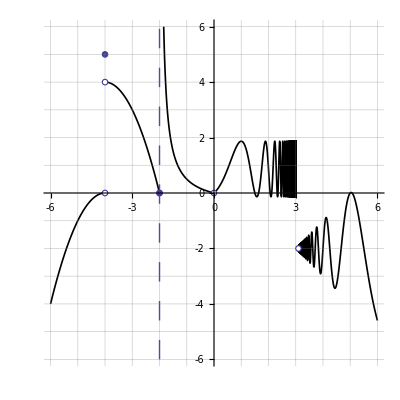

pw1.pdf

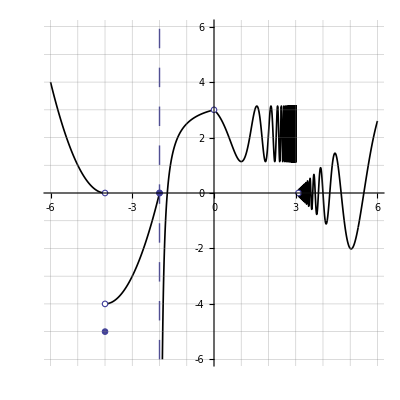

pw2.pdf

```mathematica
SetDirectory[NotebookDirectory[]]

f[x_]:=Piecewise[{
{-(x+2)^2,x<-2},
{5,x==-2},
{-(x+2)^2+4,-2<x≤0},
{1/x+1/2-1,x<2},
{Sin[5Pi/(-x+5)]+1-Sin[5Pi/(-2+5)]-1,5>x>2},
{Sin[5Pi/(-x+5)](-x+5)-2,x>5.1}
},Indeterminate]

PlotPiecewise[f[x+2],{x,-6,6},"DotSize"->0.1,PlotStyle->{Thickness[0.003],Black},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-6,6},{-6,6}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16]]
Export["pw1.pdf",%]

f[x_]:=Piecewise[{
{-(x+2)^2,x<-2},
{5,x==-2},
{-(x+2)^2+4,-2<x≤0},
{1/x+1/2-1-3,x<2},
{Sin[5Pi/(-x+5)]+1-Sin[5Pi/(-2+5)]-1-3,5>x>2},
{Sin[5Pi/(-x+5)](-x+5)-2+2,x>5.1}
},Indeterminate]

PlotPiecewise[-f[x+2],{x,-6,6},"DotSize"->0.1,PlotStyle->{Thickness[0.003],Black},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-6,6},{-6,6}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16]]
Export["pw2.pdf",%]
```

```mathematica
Sin[5Pi/(-x+5)]+1-Sin[5Pi/(-2+5)]-1/.x->2
```

0

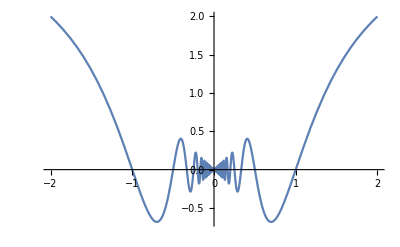

```mathematica
Plot[Sin[Pi/x]x,{x,-2,2}]
```

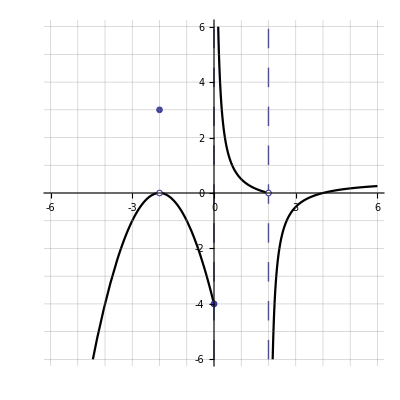

pw1.pdf

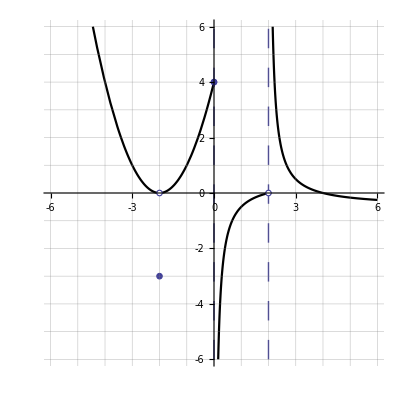

pw2.pdf

```mathematica
PlotPiecewise[Piecewise[{
{-(x+2)^2,x<-2},
{3,x==-2},
{-(x+2)^2,-2<x<=0},
{1/x-1/2,0<x<2},
{-1/(x-2)+1/2,x>2}
}
,Indeterminate],{x,-6,6},"DotSize"->0.1,PlotStyle->{Black},AspectRatio->Automatic,PlotRange->{{-6,6},{-6,6}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]}]
Export["pw1.pdf",%]
PlotPiecewise[-Piecewise[{
{-(x+2)^2,x<-2},
{3,x==-2},
{-(x+2)^2,-2<x<=0},
{1/x-1/2,0<x<2},
{-1/(x-2)+1/2,x>2}
}
,Indeterminate],{x,-6,6},"DotSize"->0.1,PlotStyle->{Black},AspectRatio->Automatic,PlotRange->{{-6,6},{-6,6}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]}]
Export["pw2.pdf",%]
```

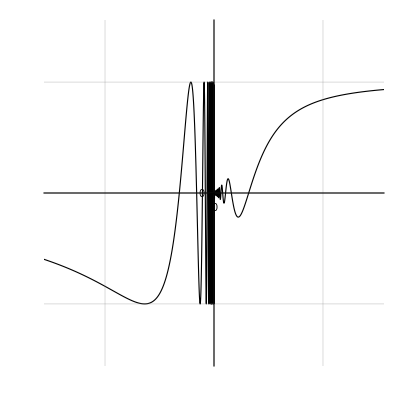

pw2.pdf

```mathematica
Plot[Piecewise[{
{Sin[1/x],x<0},
{x Sin[1/x],x>0}
}
,Indeterminate],{x,-3,3},PlotPoints->1000,PlotStyle->{Thickness[0.002],Black},AspectRatio->Automatic,PlotRange->{{-1.5,1.5},{-1.5,1.5}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]}]
Export["pw2.pdf",%]
```

/Users/ant/Sites/JumpStartIM/assets/images/functions

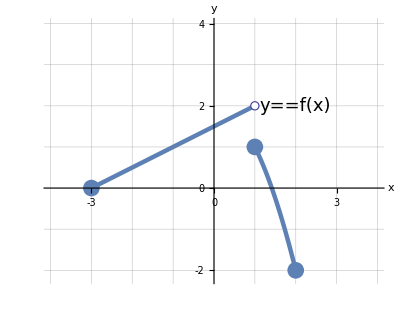

{pwgraph.svg,pwgraph.pdf}

```mathematica
SetDirectory[NotebookDirectory[]]
f[x_]:=Piecewise[{
{x/2+3/2,-3<=x<1},
{2-x^2,2>=x>=1}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,6},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-4,4},{-2.2,4}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],ListPlot[{{1,1},{-3,0},{2,-2}},PlotStyle->PointSize[0.03]]]
Export[{"pwgraph.svg","pwgraph.pdf"},%]
```

/Users/ant/Sites/JumpStartIM/assets/images/functions

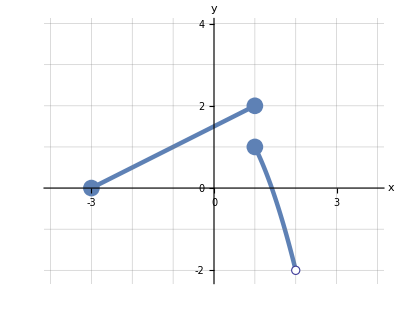

{pwgraph-bad.svg,pwgraph-bad.pdf}

```mathematica
SetDirectory[NotebookDirectory[]]
f[x_]:=Piecewise[{
{x/2+3/2,-3<=x<=1},
{2-x^2,2>x>=1}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,6},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-4,4},{-2.2,4}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16]],
ListPlot[{{1,1},{1,2},{-3,0}},PlotStyle->PointSize[0.03]]]
Export[{"pwgraph-bad.svg","pwgraph-bad.pdf"},%]
```

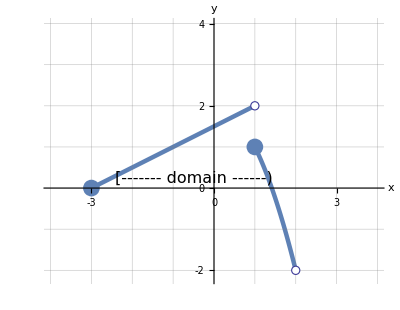

{pwgraph-domain.svg,pwgraph-domain.pdf}

```mathematica
f[x_]:=Piecewise[{
{x/2+3/2,-3<=x<1},
{2-x^2,2>x>=1}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,6},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-4,4},{-2.2,4}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],

ListPlot[{{1,1},{-3,0}},PlotStyle->PointSize[0.03]],
(*NumberLinePlot[-3<=x<2,{x,-4,4},Spacings->-0,PlotStyle->{Thickness[0.01],Blue,Opacity[0.5]}],*)
Epilog->{{Text[Style[Highlighted["[------- domain ------)"],16],{-0.5,0.25}]}}
]
Export[{"pwgraph-domain.svg","pwgraph-domain.pdf"},%]
```

```mathematica
""
```

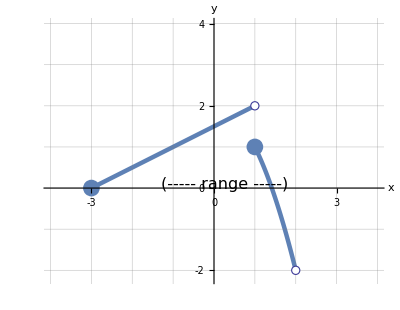

{pwgraph-range.svg,pwgraph-range.pdf}

```mathematica
f[x_]:=Piecewise[{
{x/2+3/2,-3<=x<1},
{2-x^2,2>x>=1}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,6},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-4,4},{-2.2,4}},GridLines->{Range[-6,6]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],

ListPlot[{{1,1},{-3,0}},PlotStyle->PointSize[0.03]],
Epilog->{{Rotate[Text[Style[Highlighted["(----- range -----)"],16],{0.25,0.09}],Pi/2]}}
]
Export[{"pwgraph-range.svg","pwgraph-range.pdf"},%]
```

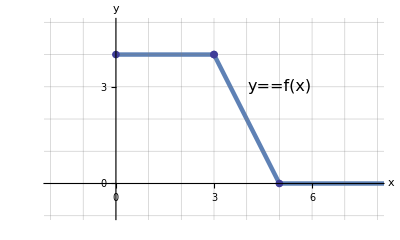

{pwgraph-ex1-all.svg,pwgraph-ex1-all.pdf}

```mathematica
f[x_]:=Piecewise[{
{4,0<=x<3},
{-2(x-5),3<=x<5},
{0,5<=x}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-2,8},{-1,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],
Epilog->{Text[Style[HoldForm[y==f[x]],16],{5,3}]}(*{{Rotate[Text[Style[Highlighted["(----- range -----)"],16],{0.25,0.09}],Pi/2]}}
*)]
Export[{"pwgraph-ex1-all.svg","pwgraph-ex1-all.pdf"},%]
```

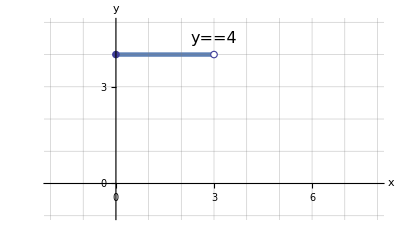

{pwgraph-ex1-1.svg,pwgraph-ex1-1.pdf}

```mathematica
f[x_]:=Piecewise[{
{4,0<=x<3}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-2,8},{-1,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],
Epilog->{Text[Style[HoldForm[y==4],16],{3,4.5}]}(*{{Rotate[Text[Style[Highlighted["(----- range -----)"],16],{0.25,0.09}],Pi/2]}}
*)]
Export[{"pwgraph-ex1-1.svg","pwgraph-ex1-1.pdf"},%]
```

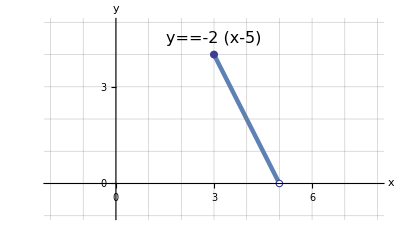

{pwgraph-ex1-2.svg,pwgraph-ex1-2.pdf}

```mathematica
f[x_]:=Piecewise[{
{-2(x-5),3<=x<5}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-2,8},{-1,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],
Epilog->{Text[Style[HoldForm[y==-2(x-5)],16],{3,4.5}]}(*{{Rotate[Text[Style[Highlighted["(----- range -----)"],16],{0.25,0.09}],Pi/2]}}
*)]
Export[{"pwgraph-ex1-2.svg","pwgraph-ex1-2.pdf"},%]
```

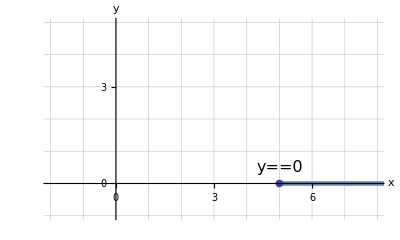

{pwgraph-ex1-3.svg,pwgraph-ex1-3.pdf}

```mathematica
f[x_]:=Piecewise[{
{0,5<=x}
},Indeterminate]
Show[PlotPiecewise[f[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-2,8},{-1,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{
Text[
Style[
HoldForm[y==f[x]],18],{2,2}]}],
Epilog->{Text[Style[HoldForm[y==0],16],{5,0.5}]}(*{{Rotate[Text[Style[Highlighted["(----- range -----)"],16],{0.25,0.09}],Pi/2]}}
*)]
Export[{"pwgraph-ex1-3.svg","pwgraph-ex1-3.pdf"},%]
```

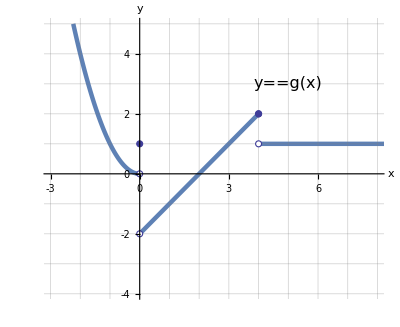

{pwgraph-ex2-all.svg,pwgraph-ex2-all.pdf}

```mathematica
g[x_]:=Piecewise[{
{x^2,x<0},
{x-2,0<x<=4}
},1]
Show[PlotPiecewise[g[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-3,8},{-4,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 14],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{Text[Style[HoldForm[y==g[x]],16],{5,3}]}]]
Export[{"pwgraph-ex2-all.svg","pwgraph-ex2-all.pdf"},%]
```

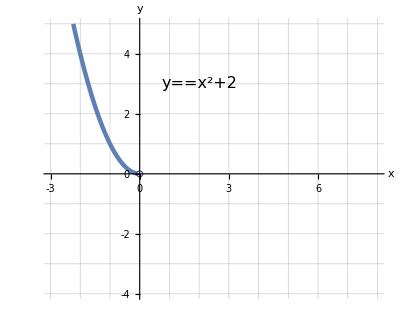

{pwgraph-ex2-1.svg,pwgraph-ex2-1.pdf}

```mathematica
g[x_]:=Piecewise[{
{x^2,x<0}
},Indeterminate]
Show[PlotPiecewise[g[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-3,8},{-4,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 14],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{Text[Style[HoldForm[y==x^2+2],16],{2,3}]}]]
Export[{"pwgraph-ex2-1.svg","pwgraph-ex2-1.pdf"},%]
```

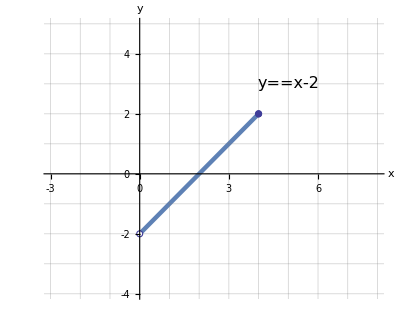

{pwgraph-ex2-2.svg,pwgraph-ex2-2.pdf}

```mathematica
g[x_]:=Piecewise[{
{x-2,0<x<=4}
},Indeterminate]
Show[PlotPiecewise[g[x],{x,-6,10},"DotSize"->0.1,PlotStyle->{Thickness[0.008]},AspectRatio->Automatic,PlotPoints->10000,PlotRange->{{-3,8},{-4,5}},GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 14],AxesLabel->{x,y},AxesStyle->Directive[16],
Epilog->{Text[Style[HoldForm[y==x-2],16],{5,3}]}]]
Export[{"pwgraph-ex2-2.svg","pwgraph-ex2-2.pdf"},%]
```

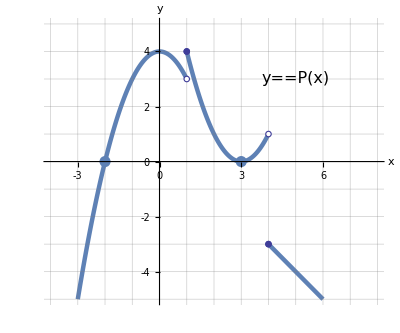

{pwgraph-ex3.svg,pwgraph-ex3.pdf}

```mathematica
f[x_]:=Piecewise[{
{4-x^2,-4<=x<1},
{(x-3)^2,1<=x<4},
{1-x,4<=x}
},Indeterminate]
Show[
PlotPiecewise[f[x],
{x,-10,10},
"DotSize"->0.1,
PlotStyle->{Thickness[0.008]},
AspectRatio->Automatic,
PlotPoints->10000,
PlotRange->{{-4,8},{-5,5}},
GridLines->{Range[-6,8]},Ticks->{Range[-6,6]},TicksStyle->Directive["Label", 16],
AxesLabel->{x,y},
AxesStyle->Directive[16],
Epilog->{Text[Style[HoldForm[y==P[x]],16],{5,3}]}],
ListPlot[{{-2,0},{3,0}},PlotStyle->PointSize[0.02]]]
Export[{"pwgraph-ex3.svg","pwgraph-ex3.pdf"},%]
```